```mathematica
s[x_]:=Abs[x-Round[x]]
```

```mathematica
saw[n_,x_] := s[2^n x]/2^n
```

```mathematica
bl[x_]:=Sum[saw[n,x],{n,0,100}]
```

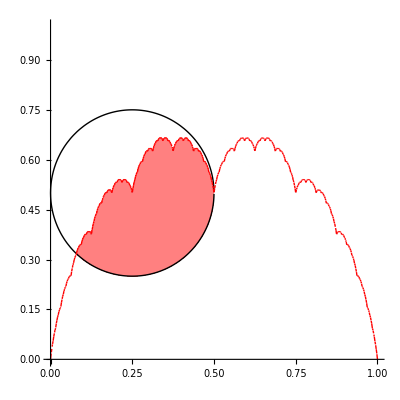

```mathematica
Plot[{y/.ToRules@First@Reduce[(x-1/4)^2+(y-1/2)^2==(1/4^2),y],y/.ToRules@Last@Reduce[(x-1/4)^2+(y-1/2)^2==(1/4^2),y],Sum[saw[n,x],{n,0,8}]},{x,0,1},PlotStyle->{Black,Black,Red},PlotRange->{0,1},AspectRatio->1,Filling->{1->{{3},{Pink,None}}},PerformanceGoal->"Quality"]
```

```mathematica
FindRoot[(x-(1/4))^2+(y-(1/2))^2==(1/4)^2/.y->bl[x],{x,0.075}]
```

{x→0.0789078}

```mathematica
areaUnderCircle=NIntegrate[y/.ToRules@First@Reduce[(x-1/4)^2+(y-1/2)^2==(1/4)^2,y],{x,0.0789077853183414,1/2},WorkingPrecision->20]
```

0.1223107315657338687

```mathematica
bla=NIntegrate[bl[x],{x,0,0.0789077853183414},AccuracyGoal->8,WorkingPrecision->20,MaxRecursion->50]
```

```mathematica
bla=15/128+7/128+Sum[3/2^(n+5),{n,2,Infinity}]
```

7/32

```mathematica
N[1/4-bla-areaUnderCircle,8]
```

0.11316016

```mathematica
i[x_,lev_]:=Piecewise[{{0,lev>200},{1/2+i[x-1,lev+1],x≥1},{1/2-i[1-x,lev+1], x>1/2},{i[2x,lev+1]/4+x^2/2,True}}]
```

```mathematica
ia=i[0.0789077853183414,0]
```

0.0145291

```mathematica
1/4-ia-areaUnderCircle
```

```mathematica
0.11316016951844442
```